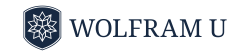

# Introduction to Quantum Computing

## Lesson 3: Bloch Sphere

## Overview

The Bloch vector is a geometric representation of a single qubit state. Each qubit state corresponds to a point inside a three-dimensional unit sphere. Points on the surface of the sphere represent pure states, while points strictly inside the sphere represent mixed states. The Bloch vector itself can be expressed either in Cartesian coordinates or in spherical coordinates, depending on which description is more convenient.

## Bloch Sphere

Qubits are not classical bits, so listing classical bitstrings does not capture all possible qubit states. How are quantum states represented instead? Let’s begin with some visual intuition. There is a very useful graphical representation of 1-qubit states called the Bloch sphere. The Bloch sphere is named after physicist Felix Bloch:

-Graphics-

In this approach, a quantum state is represented by a point in 3D space inside a sphere of radius 1 (the Bloch sphere). The point may lie on the surface, in which case we call it a pure state, or inside the sphere, in which case we call it a mixed state.

Show the Bloch vector of 0:

```mathematica
QuantumState["0"]["BlochVector"]
```

{0,0,1}

Show the Bloch vector of 1:

```mathematica
QuantumState["1"]["BlochVector"]
```

{0,0,-1}

Show the Bloch vector of cos(π/6)0+ⅇ^(-ⅈπ/4)sin(π/6)1:

```mathematica
QuantumState[{Cos[π/6],ⅇ^(-ⅈ π/4)Sin[π/6]}]["BlochVector"]//FullSimplify
```

{(√(3/2))/2,-(√(3/2))/2,1/2}

## Spherical and Cartesian Coordinates of Bloch Sphere

The Bloch vector is represented as {r_x,r_y,r_z} such that r_x^2+r_y^2+r_z^2<=1. In the spherical coordinates, it is described by three variables {r,θ,ϕ} and its Cartesian coordinates are given by r{Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ],Cos[θ]}.

```mathematica
FromSphericalCoordinates[{r,θ,ϕ}]
```

{r Cos[ϕ] Sin[θ],r Sin[θ] Sin[ϕ],r Cos[θ]}

```mathematica
ToSphericalCoordinates[{x,y,z}]
```

{√(x^2+y^2+z^2),ArcTan[z,√(x^2+y^2)],ArcTan[x,y]}

All points in the Bloch sphere are accessible, given different values of r, θ, and ϕ:

```mathematica
Manipulate[
[r{Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ],Cos[θ]},"Labels"->"Optics",PlotLabel->"Bloch vector Cartesian coordinates\n"<>ToString[Round[r{Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ],Cos[θ]},.01]]<>"\n",ImageSize->250],{{ϕ,π/3},0,2π},{{θ,π/4},0,π},{{r,1},0,1},SaveDefinitions:>True]
```

## Common Notations in Bloch Sphere

The states labeled +, -, L and R are other specific states the qubits can attain. However, the 0 and 1 states are usually called the computational basis states. The use of the sphere already suggests that the space of 1-qubit states is already quite a bit richer than only 0 or 1 as in classical bits.

Show the Bloch vector of 0:

```mathematica
QuantumState["0"]["BlochPlot",ImageSize->200]
```

-Graphics3D-

Show the Bloch vector of 1:

```mathematica
QuantumState["1"]["BlochPlot",ImageSize->200]
```

-Graphics3D-

Show the Bloch vector of +:

```mathematica
QuantumState["+"]["BlochPlot",ImageSize->200]
```

-Graphics3D-

Show the Bloch vector of -:

```mathematica
QuantumState["-"]["BlochPlot",ImageSize->200]
```

-Graphics3D-

Show the Bloch vector of R:

```mathematica
QuantumState["R"]["BlochPlot",ImageSize->200]
```

-Graphics3D-

Show the Bloch vector of L:

```mathematica
QuantumState["L"]["BlochPlot",ImageSize->200]
```

-Graphics3D-

## Summary

The Bloch sphere is a unit sphere used to represent qubit states.

A qubit state lies either on the surface or inside this sphere. States on the surface are called pure states, while states inside the sphere are mixed states.

The Bloch vector itself is a point in three-dimensional space, and it can be written either in Cartesian coordinates or in spherical coordinates; both descriptions are commonly used in quantum computing.